```mathematica
Clear["Global`*"];
SeedRandom[0];
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
σ=0.00001;
U[x_]=x^2/(2 σ^2);
dU[x_]=GradientG[U[x],{x}];
ddU[x_]=HessianH[U[x],{x}];
```

```mathematica
QS=hmc[U,dU,ddU,1,5000,10000,True,True];
```

501 68.1874 3.45642 0.8494 0.247644 5.54857 73.7359 78.1559 1.89059×10^-7 0.0251638 True {1,9,11} {1,10,11}

1002 36.2281 2.47035×10^-10 0.489306 0.346944 7.84659 70.284 44.0747 4.45792×10^-7 0.0445792 False {1,2,5,11} {1,11}

1503 65.8138 2.33788 0.622839 0.391509 4.47019 70.284 48.045 3.68423×10^-7 0.0490371 True {1,3,5,6,11} {1,11}

2004 41.8846 8.30107×10^-10 0.720258 0.300238 6.16042 70.284 48.045 4.05265×10^-7 0.0490371 False {1,3,4,6,8,11} {1,11}

2505 68.1232 3.95163 0.64047 0.413492 2.16082 70.284 52.3402 4.90371×10^-7 0.0405265 True {1,2,3,5,6,11} {1,11}

3006 50.7452 4.7703×10^-10 0.748559 0.380863 6.17873 67.4863 56.9239 3.3493×10^-7 0.0405265 False {1,3,4,5,10,11} {1,11}

$Aborted

```mathematica
StandardDeviation[QS]
```

{9.50892×10^-6}

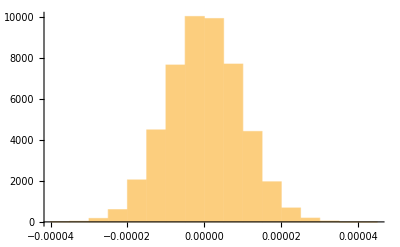

```mathematica
Histogram[QS[[;;,1]]]
```